```mathematica
ParabolaArcLength[a_,l_]=Refine[Integrate[√(1.+(2. a x)^2),{x,-l/2.,l/2.}],{a>0.,l>0.}];
```

```mathematica
ParabolaLowerArea[a_,l_]=Integrate[a x^2,{x,-l/2.,l/2.}];
```

```mathematica
ParabolaUpperArea[a_,l_]:=l a (l/2.)^2-ParabolaLowerArea[a,l]
```

```mathematica
Clear[ParabolaWidth]
ParabolaWidth[W_?NumericQ,a_?NumericQ]:=l/.FindRoot[W==ParabolaArcLength[a,l],{l,W/10.}]
```

```mathematica
ParabolaWidth[L,a]
```

ParabolaWidth[L,a]

```mathematica
ParabolaArea[W_,a_]:=ParabolaUpperArea[a,ParabolaWidth[W,a]]
```

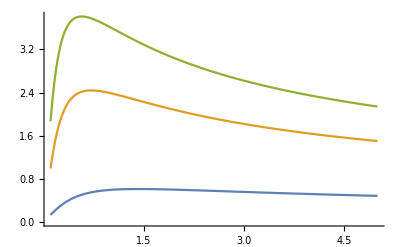

```mathematica
Plot[{ParabolaArea[2,a],ParabolaArea[4,a],ParabolaArea[5,a]},{a,.1,5}]
```

```mathematica
Maximize[ParabolaArea[2,a],a]
```

{0.609787,{a→1.41922}}

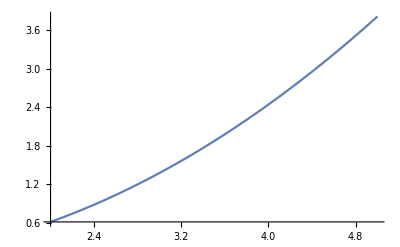

```mathematica
Plot[Maximize[ParabolaArea[W,a],a][[1]],{W,2,5}]
```

```mathematica
ParabolaOptimizedArea[W_]:=Maximize[ParabolaArea[W,a],a][[1]]
TotalArea[H_?NumericQ,W_?NumericQ]:=Maximize[H *ParabolaWidth[W,a] +2 ParabolaArea[W,a],a]
ParabolaA[H_,W_]=TotalArea[H,W][[2,1,2]]
BaffleHeight[H_?NumericQ,W_?NumericQ]:=H+
```

```mathematica
d=3
Ar=TotalArea[d,5]
li=ParabolaWidth[5,Ar[[2,1,2]]]
arc2length=Table[{i,ParabolaWidth[i,TotalArea[d,i][[2,1,2]]]},{i,1,8,.1}];
```

3

{19.4042,{a→0.246317}}

4.29686

```mathematica
rect2real=Table[Table[{i,TotalArea[d,i][[1]]/(d*i)},{i,1,8,.1}],{d,1,4,.5}];
```

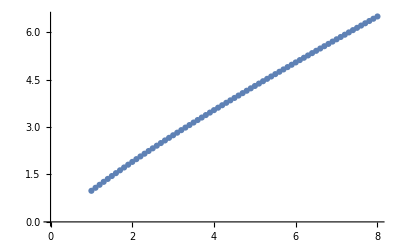

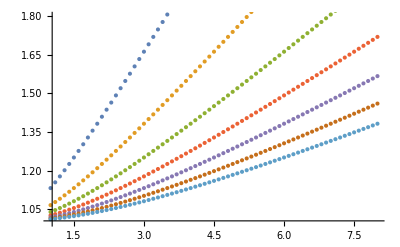

```mathematica
ListPlot[arc2length]
ListPlot[rect2real,PlotRange->{{1,8},{1,1.8}}]
```

```mathematica
H=3;
W=5;
```

0.246317

0.246317

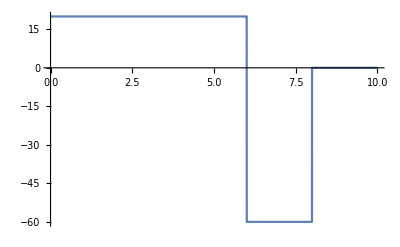

```mathematica
g[x_]:=[{{20,x<6},{-60,6<x<8},{}}]
Plot[g[x],{x,0,10},Exclusions->None]
```

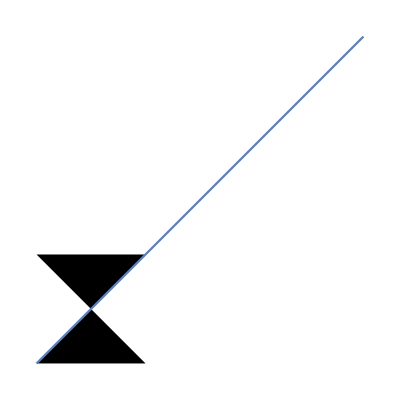

```mathematica
p=Graphics[Polygon[{{0,0},{1,1},{0,1},{1,0}}]];
q=Plot[x,{x,0,3}];
Show[p,q]
```

```mathematica
a={{0,0},{1,1}};
b={{2,2},{3,3}};
c=Join[a,b]
```

{{0,0},{1,1},{2,2},{3,3}}

```mathematica
aa[xa_]:=xa^2
aa[Range[5]]
```

{1,4,9,16,25}

```mathematica
TotalArea[5,2]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {l} = {0.2}.

ReplaceAll::reps: {FindRoot[2==ParabolaArcLength[0,l],{l,2/10.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Maximize::ivar: 0 is not a valid variable.

Part::partd: Part specification Maximize[0.+5 (l/.FindRoot[2==ParabolaArcLength[«2»],{l,Times[«2»]}]),0]⟦2,1,2⟧ is longer than depth of object.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {l} = {0.2}.

ReplaceAll::reps: {FindRoot[2==ParabolaArcLength[0,l],{l,2/10.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Maximize::ivar: 0 is not a valid variable.

Part::partd: Part specification Maximize[0.+5 (l/.FindRoot[2==ParabolaArcLength[«2»],{l,Times[«2»]}]),0]⟦2,1,2⟧ is longer than depth of object.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {l} = {0.2}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[2==ParabolaArcLength[0,l],{l,2/10.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Maximize::ivar: 0 is not a valid variable.

General::stop: Further output of Maximize::ivar will be suppressed during this calculation.

Part::partd: Part specification Maximize[0.+5 (l/.FindRoot[2==ParabolaArcLength[«2»],{l,Times[«2»]}]),0]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{10.2533,{Maximize[0.+5 (l/.FindRoot[2==ParabolaArcLength[0,l],{l,2/10.}]),0]⟦2,1,2⟧→0.194071}}